```mathematica
(* Filename: Plot_example_in_experiment_1.nb *)
(* Ver. 1 (21-Sep-2023) *)
(*****)
(* Ver. 0 (25-Apr-2023) *)
(*
This file is a program code in Mathematica to get plots in numerical experinemt 1.
*)
```

```mathematica
nn=2;
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "experiment_1". *****)
datadir= "D:/.../experiment_1";
```

```mathematica
mydirRefSol = StringJoin[datadir,"/By_wo2_Ef_AstabExpRK3/Set16_Tr10000_Batch6400/Ref"];
mydirA = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al/s=3/Set16_Tr10000_Batch6400"];
mydirB = StringJoin[datadir,"/By_wo2_srock2_Ab_values/s=3/Set16_Tr10000_Batch6400"];
mydirC = StringJoin[datadir,"/By_wo2_SSDFMT/Set16_Tr10000_Batch6400"]; 
mydirD = StringJoin[datadir,"/By_wo2_Ef_AstabExpRK3/Set16_Tr10000_Batch6400"];
```

```mathematica
steplogleng=5; 
stepPlotStart=1;
```

```mathematica
numSet=16;
ydim=nn;
```

```mathematica
dataA=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA[[ii]]=Import[mydirA<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA[[ii]][[1,2]] += Import[StringJoin[mydirA,filename[ii]],"Table"][[1,2]];
];
dataA[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataB=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB[[ii]]=Import[mydirB<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB[[ii]][[1,2]] += Import[StringJoin[mydirB,filename[ii]],"Table"][[1,2]];
];
dataB[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataC=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataC[[ii]]=Import[mydirC<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataC[[ii]][[1,2]] += Import[StringJoin[mydirC,filename[ii]],"Table"][[1,2]];
];
dataC[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataD=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataD[[ii]]=Import[mydirD<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataD[[ii]][[1,2]] += Import[StringJoin[mydirD,filename[ii]],"Table"][[1,2]];
];
dataD[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataRef=Table[{},{ii,1,ydim}];
meanRef=Table[1,{ii,1,ydim}];
stdDevRef=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataRef[[ii]]=Append[dataRef[[ii]],Import[mydirRefSol<>filename[ii],"Table"][[1,2]]];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataRef[[ii]] =Append[dataRef[[ii]], Import[mydirRefSol<>filename[ii],"Table"][[1,2]]];
];
meanRef[[ii]]= Mean[dataRef[[ii]]];
stdDevRef[[ii]]= StandardDeviation[dataRef[[ii]]];
];
```

```mathematica
exactTmp=meanRef;
ExactOdeExp=Table[1,{ii,1,ydim}];
For[ii=1,ii≤ydim, ii++,
ExactOdeExp[[ii]]={};
For[jj=1,jj≤steplogleng,jj++,ExactOdeExp[[ii]]=Append[ExactOdeExp[[ii]],{-jj,exactTmp[[ii]]}];
];
];
```

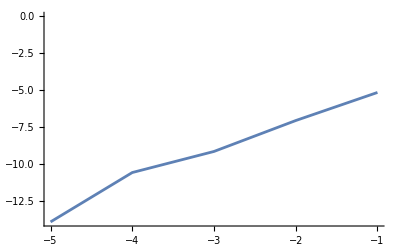

```mathematica
difflistA={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistA=Append[difflistA,{dataA[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotExpA=ListPlot[difflistA,Joined->True]
```

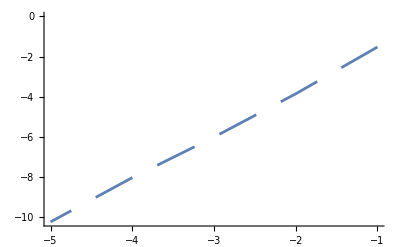

```mathematica
difflistB={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistB=Append[difflistB,{dataB[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotExpB=ListPlot[difflistB,Joined->True,PlotStyle->Dashing[{0.075,0.05}]]
```

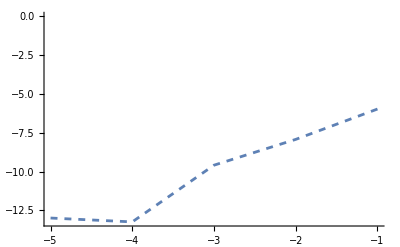

```mathematica
difflistC={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistC=Append[difflistC,{dataC[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataC[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotExpC=ListPlot[difflistC,Joined->True,PlotStyle->Dashed]
```

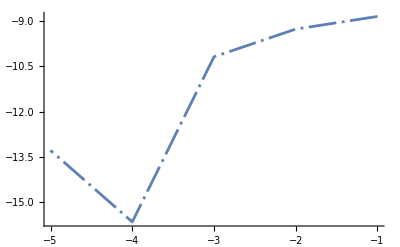

```mathematica
difflistD={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistD=Append[difflistD,{dataD[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataD[[id]]⟦i,2⟧-ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeExp[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotExpD=ListPlot[difflistD,Joined->True,PlotStyle->{Dashing[{0.05,0.01,0.005,0.01}]}(*DotDashed*)]
```

```mathematica
dataA=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataA[[ii]]=Import[mydirA<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataA[[ii]][[1,2]] += Import[StringJoin[mydirA,filename[ii]],"Table"][[1,2]];
];
dataA[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataB=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataB[[ii]]=Import[mydirB<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataB[[ii]][[1,2]] += Import[StringJoin[mydirB,filename[ii]],"Table"][[1,2]];
];
dataB[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataC=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataC[[ii]]=Import[mydirC<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataC[[ii]][[1,2]] += Import[StringJoin[mydirC,filename[ii]],"Table"][[1,2]];
];
dataC[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataD=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataD[[ii]]=Import[mydirD<>filename[ii],"Table"];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataD[[ii]][[1,2]] += Import[StringJoin[mydirD,filename[ii]],"Table"][[1,2]];
];
dataD[[ii]][[1,2]] /= numSet;
];
```

```mathematica
dataRef=Table[{},{ii,1,ydim}];
meanRef=Table[1,{ii,1,ydim}];
stdDevRef=Table[1,{ii,1,ydim}];
For[ii=1, ii<=ydim, ii++,
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
dataRef[[ii]]=Append[dataRef[[ii]],Import[mydirRefSol<>filename[ii],"Table"][[1,2]]];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
dataRef[[ii]] =Append[dataRef[[ii]], Import[mydirRefSol<>filename[ii],"Table"][[1,2]]];
];
meanRef[[ii]]= Mean[dataRef[[ii]]];
stdDevRef[[ii]]= StandardDeviation[dataRef[[ii]]];
];
```

```mathematica
exactTmp=meanRef;
ExactOdeDis=Table[1,{ii,1,ydim}];
For[ii=1,ii≤ydim, ii++,
ExactOdeDis[[ii]]={};
For[jj=1,jj≤steplogleng,jj++,ExactOdeDis[[ii]]=Append[ExactOdeDis[[ii]],{-jj,exactTmp[[ii]]}];
];
];
```

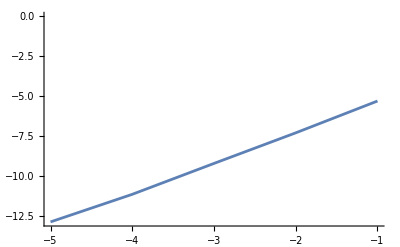

```mathematica
difflistA={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistA=Append[difflistA,{dataA[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataA[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotDisA=ListPlot[difflistA,Joined->True]
```

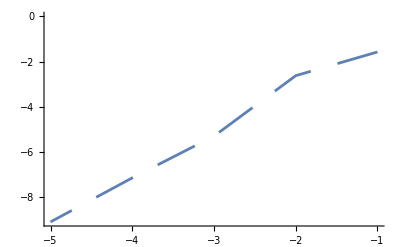

```mathematica
difflistB={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistB=Append[difflistB,{dataB[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataB[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotDisB=ListPlot[difflistB,Joined->True,PlotStyle->Dashing[{0.075,0.05}]]
```

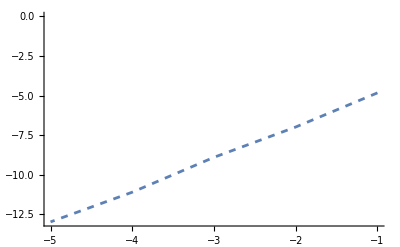

```mathematica
difflistC={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistC=Append[difflistC,{dataC[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataC[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotDisC=ListPlot[difflistC,Joined->True,PlotStyle->Dashed]
```

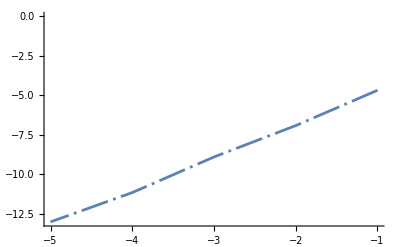

```mathematica
difflistD={};
For[i=stepPlotStart,i≤steplogleng,i++,difflistD=Append[difflistD,{dataD[[1]]⟦i,1⟧,Log[2,(√(Sum[(dataD[[id]]⟦i,2⟧-ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))/(√(Sum[(ExactOdeDis[[id]]⟦i,2⟧)^2,{id,1,ydim}]))]}];
];
tmpPlotDisD=ListPlot[difflistD,Joined->True,PlotStyle->{Dashing[{0.05,0.01,0.005,0.01}]}(*DotDashed*)]
```

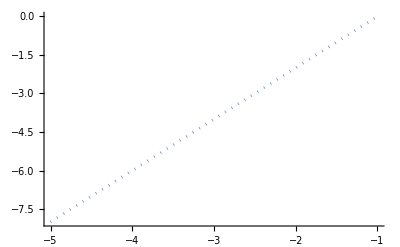

```mathematica
tmpRefSlope2=Plot[2x+2,{x,-5,-1},PlotStyle->Dotted]
```

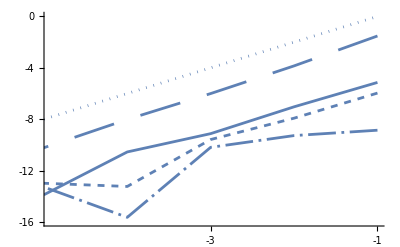

```mathematica
ll=0.015;(* 0.03, 0.015 *)
Show[tmpPlotExpA,tmpPlotExpB,tmpPlotExpC,tmpPlotExpD,tmpRefSlope2,PlotRange->{{-steplogleng+0.08,-1},{-16,0}},AxesOrigin->{-steplogleng,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,1,6}],Union[Table[{-2ii,ToString[-2ii],ll},{ii,-1,10}],{{0,"0",ll}}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

```mathematica
tmpRefSlope2=Plot[2x+2,{x,-5,-1},PlotStyle->Dotted]
```

-Graphics-

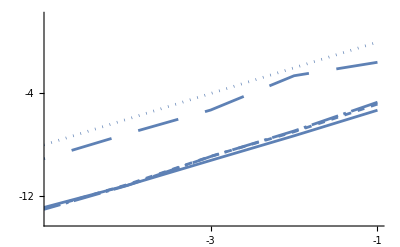

```mathematica
Show[tmpPlotDisA,tmpPlotDisB,tmpPlotDisC,tmpPlotDisD,tmpRefSlope2,PlotRange->{{-steplogleng+0.08,-1},{-14,2}},AxesOrigin->{-steplogleng,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,1,6}],Union[Table[{-2ii,ToString[-2ii],ll},{ii,1,10}],{{0,"0",ll}},Table[{2ii,ToString[2ii],ll},{ii,1,10}]]},BaseStyle->{14,FontFamily->"Helvetica"}]
```